## Singular Perturbation

```mathematica
eq:={0.01 y''[t]+3y'[t]-(y[t])^4==0,y[0]==1,y[1]==1}
```

```mathematica
NDSolve[eq,y[t],{t,0,1}]
```

{{y[t]→InterpolatingFunction[…][t]}}

```mathematica
{yans[t_]}={y[t]}/.Flatten[NDSolve[eq,y[t],{t,0,1}]]
```

{InterpolatingFunction[…][t]}

```mathematica
graphy=Plot[yans[t],{t,0,1},AxesLabel->{"x","y"},PlotLabel->"Numerical Solution of y"];
```

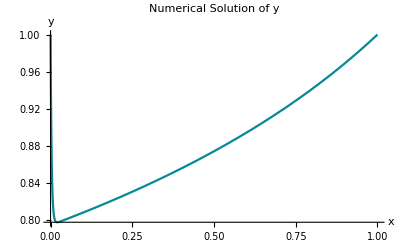

```mathematica
Show[graphy]
```

```mathematica
yhand[x_]:=1/(2-x)^(1/3)+(1-1/2^(1/3)  ) ⅇ^((-3x)/0.01)
```

```mathematica
graphyh=Plot[yhand[x],{x,0,1},AxesLabel->{"t","y"},PlotLabel->"Analytic Solution of y"];
```

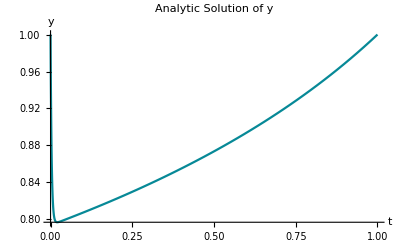

```mathematica
Show[graphyh]
```

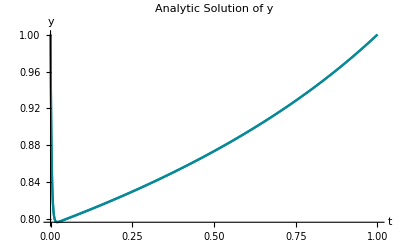

```mathematica
Show[graphyh,graphy]
```